# N2 Spectroscopy

```mathematica
(*define contants*)
h = 6.62607015* 10^−34;
c = 3 * 10 ^8;
eVconversion = 6.241509*10^18;
nanoConversion = 10^-9;
μ = 1.16 * (10^-26);
```

#### ROOMLIGHT

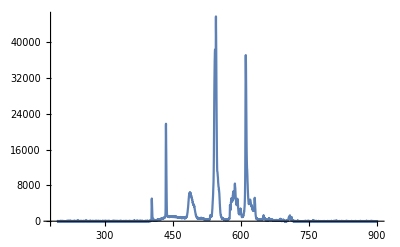

```mathematica
inputFilePath = "/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_09-33-43-465.txt";
fileContent=Drop[Import[inputFilePath,"Table"],14];
wavelength = fileContent[[All,1]];
spectral = fileContent[[All,2]];
ListLinePlot[fileContent,PlotRange -> All]
```

```mathematica
FindPeaks[spectral,0,0,5000]
```

{{974,5064.74},{1125,21771.3},{1380,6364.66},{1384,6354.07},{1386,6375.26},{1388,6396.46},{1390,6253.39},{1395,5797.71},{1398,5691.74},{1400,5548.68},{1404,5174.24},{1662,38336.5},{1664,37725.4},{1672,45744.},{1706,7064.08},{1848,5181.31},{1862,5656.42},{1868,6673.75},{1870,6551.88},{1878,5218.4},{1886,8415.23},{1915,5017.05},{2010,37105.4},{2114,5236.06}}

```mathematica
wavelength[[974]]
wavelength[[1125]]
wavelength[[1380]]
wavelength[[1662]]
 wavelength[]
 wavelength[[1868]]
```

403.903

435.111

487.048

543.33

583.652

583.652

#### UNSATURATED HYDROGEN

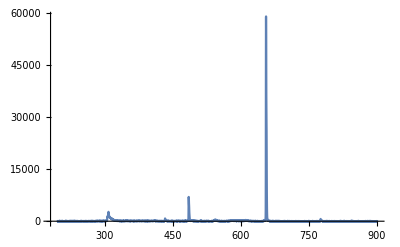

```mathematica
inputFilePath2 = "/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_09-36-28-256.txt";
fileContent2=Drop[Import[inputFilePath2,"Table"],14];
wavelength2 = fileContent2[[All,1]];
spectral2 = fileContent2[[All,2]];
ListLinePlot[fileContent2,PlotRange -> All]
```

```mathematica
FindPeaks[spectral2,0,0,10000]
FindPeaks[spectral2,0,0,5000]
```

{{2246,59024.9}}

{{1371,6999.61},{2246,59024.9}}

```mathematica
wavelength2[[1371]]
 wavelength2[[2246]]
```

485.232

655.836

```mathematica
peak2 = {485.232 * nanoConversion,655.836 * nanoConversion}
```

{4.85232×10^-7,6.55836×10^-7}

```mathematica
deltaE2 = {((h*c)/peak2[[1]])*eVconversion, ((h*c)/peak2[[2]])*eVconversion}
```

{2.55692,1.89178}

#### Saturated Hydrogen

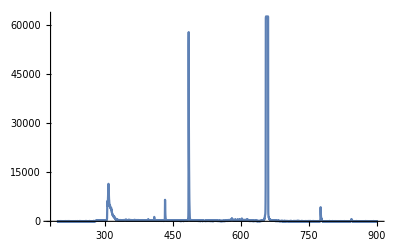

```mathematica
inputFilePath3 = "/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_09-37-14-457.txt";
fileContent3=Drop[Import[inputFilePath3,"Table"],14];
wavelength3 = fileContent3[[All,1]];
spectral3 = fileContent3[[All,2]];
ListLinePlot[fileContent3,PlotRange -> All]
```

```mathematica
FindPeaks[spectral3,0,0,2000]
```

{{511,6198.2},{517,8035.05},{521,11442.1},{536,4970.69},{1083/2,4059.33},{548,4190.02},{552,3603.64},{555,2944.85},{564,2088.24},{1115,6563.8},{1371,57704.2},{2257,62481.8},{2907,4313.66}}

```mathematica
wavelength3[[511]]
wavelength3[[1115]]
wavelength3[[1371]]
wavelength3[[2257]]
wavelength3[[2907]]
```

306.195

433.055

485.232

657.901

776.161

```mathematica
peak3 = {306.195*nanoConversion,433.055*nanoConversion,485.232 * nanoConversion,657.901 * nanoConversion,776.161*nanoConversion}
```

{3.06195×10^-7,4.33055×10^-7,4.85232×10^-7,6.57901×10^-7,7.76161×10^-7}

```mathematica
deltaE3 = {((h*c)/peak3[[1]])*eVconversion, ((h*c)/peak3[[2]])*eVconversion,((h*c)/peak3[[3]])*eVconversion, ((h*c)/peak3[[4]])*eVconversion,((h*c)/peak3[[5]])*eVconversion }
```

{4.05199,2.86499,2.55692,1.88585,1.59851}

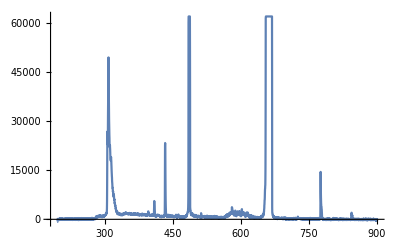

```mathematica
inputFilePath4 = "/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_09-37-44-257.txt";
fileContent4=Drop[Import[inputFilePath4,"Table"],14];
wavelength4 = fileContent4[[All,1]];
spectral4 = fileContent4[[All,2]];
ListLinePlot[fileContent4,PlotRange -> All]
```

```mathematica
FindPeaks[spectral4,0,0,50000]
```

{{2755/2,61859.5},{2280,61859.5}}

```mathematica
wavelength4[[521]]
```

308.336

```mathematica
wavelength4[[1000]]
```

409.3

```mathematica
wavelength4[[1116]]
```

433.26

```mathematica
wavelength4[[1370]]
```

485.03

```mathematica
wavelength4[[2280]]
```

662.212

```mathematica
peak4 = {308.336,409.3,433.26,485.03,662.212}
```

{308.336,409.3,433.26,485.03,662.212}

```mathematica
deltaE3
deltaE2
```

{4.05199,2.86499,2.55692,1.88585,1.59851}

{2.55692,1.89178}

3

2

1.88889

```mathematica
results={};

For[i=1,i<=10,i++,
For[j=1,j<=10,j++,
result=13.6*((1/(i^2))-(1/(j^2)));
If[result==2.856 ,
Print["2.856. i = ",i,", j = ",j];
];
If[result==2.55 ,
Print["2.55. i = ",i,", j = ",j];
];
If[result==1.8888888888888888 ,
Print["1.8888888888888888. i = ",i,", j = ",j];
];

AppendTo[results,result];]
;]
results
```

1.8888888888888888. i = 2, j = 3

2.55. i = 2, j = 4

2.856. i = 2, j = 5

{0.,10.2,12.0889,12.75,13.056,13.2222,13.3224,13.3875,13.4321,13.464,-10.2,0.,1.88889,2.55,2.856,3.02222,3.12245,3.1875,3.2321,3.264,-12.0889,-1.88889,0.,0.661111,0.967111,1.13333,1.23356,1.29861,1.34321,1.37511,-12.75,-2.55,-0.661111,0.,0.306,0.472222,0.572449,0.6375,0.682099,0.714,-13.056,-2.856,-0.967111,-0.306,0.,0.166222,0.266449,0.3315,0.376099,0.408,-13.2222,-3.02222,-1.13333,-0.472222,-0.166222,0.,0.100227,0.165278,0.209877,0.241778,-13.3224,-3.12245,-1.23356,-0.572449,-0.266449,-0.100227,0.,0.065051,0.10965,0.141551,-13.3875,-3.1875,-1.29861,-0.6375,-0.3315,-0.165278,-0.065051,0.,0.0445988,0.0765,-13.4321,-3.2321,-1.34321,-0.682099,-0.376099,-0.209877,-0.10965,-0.0445988,0.,0.0319012,-13.464,-3.264,-1.37511,-0.714,-0.408,-0.241778,-0.141551,-0.0765,-0.0319012,0.}

#### NITROGEN

```mathematica
inputFilePath5 = "/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_11-14-13-204.txt"
```

/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_11-14-13-204.txt

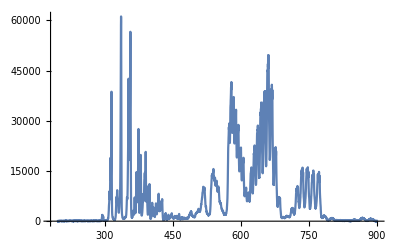

```mathematica
fileContent5=Drop[Import[inputFilePath5,"Table"],14];
wavelength5 = fileContent5[[All,1]];
spectral5= fileContent5[[All,2]];
ListLinePlot[fileContent5,PlotRange -> All]
```

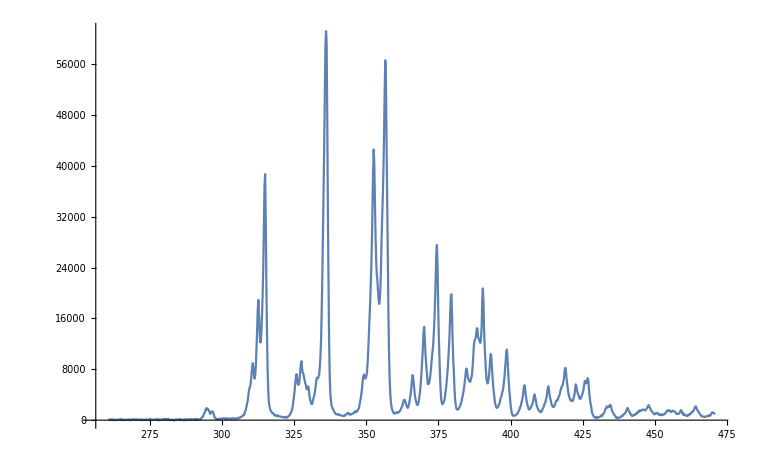

```mathematica
zoomed = fileContent5[[300;;1300]];
 wavelength5 = zoomed[[All,1]];
spectral5 = zoomed[[All,2]];
ListLinePlot[zoomed,PlotRange -> All]
```

```mathematica
FindPeaks[spectral5,0,0,12000]
```

{{242,18906.6},{253,38688.1},{352,61173.7},{430,42568.5},{449,56593.9},{513,14660.7},{534,27550.4},{558,19798.6},{600,14427.5},{610,20713.5}}

```mathematica
(*0-0*)
wavelength5[[352]] 
(*0-1*)
wavelength5[[449]]

(*0-2*)
wavelength5[[558]]

FindPeaks[spectral5,0,0,1200]
(*1-0*)
wavelength5[[253]]
(*1-1*)
wavelength5[[337]]
(*1-2*)
wavelength5[[430]]
```

336.053

356.583

379.496

{{158,1891.02},{160,1793.87},{168,1398.24},{233,8959.36},{242,18906.6},{253,38688.1},{304,7232.02},{312,9261.39},{323,5315.69},{337,6650.94},{352,61173.7},{398,1244.59},{400,1440.63},{402,1382.35},{414,7171.97},{430,42568.5},{449,56593.9},{468,1242.82},{480,3187.41},{494,7090.72},{513,14660.7},{534,27550.4},{558,19798.6},{583,8122.18},{588,6200.55},{600,14427.5},{610,20713.5},{623,10405.9},{650,11080.6},{679,5488.77},{696,4054.62},{719,5324.52},{733,3115},{748,8199.9},{759,3046.11},{765,5637.13},{781,6189.96},{785,6597.95},{817,2161.24},{820,2140.05},{823,2420.88},{852,1917.51},{871,1475.96},{873,1527.18},{877,1657.88},{879,1650.81},{881,1629.62},{888,2367.89},{920,1550.14},{922,1548.37},{924,1477.72},{926,1422.97},{929,1493.62},{943,1583.7},{961,1260.48},{968,2168.31},{996,1246.35}}

314.967

332.867

352.572

```mathematica
peak5={wavelength5[[352]]*nanoConversion, wavelength5[[449]]*nanoConversion,wavelength5[[558]]*nanoConversion};
peak5two= {wavelength5[[253]]*nanoConversion, wavelength5[[337]]*nanoConversion,wavelength5[[430]]*nanoConversion};
peak5two
peak5
```

{3.14967×10^-7,3.32867×10^-7,3.52572×10^-7}

{3.36053×10^-7,3.56583×10^-7,3.79496×10^-7}

```mathematica
e = {0,0,0}
e2 = {0,0,0}
```

{0,0,0}

{0,0,0}

3.36053×10^-7

```mathematica
e[[1]] = ( 1/ peak5[[1]]) *(10^-2);
e[[2]] = ( 1/ peak5[[2]]) *(10^-2);
e[[3]] = ( 1/ peak5[[3]]) *(10^-2);
e2[[1]] = ( 1/ peak5two[[1]]) *(10^-2);
e2[[2]] = ( 1/ peak5two[[2]]) *(10^-2);
e2[[3]] = ( 1/ peak5two[[3]]) *(10^-2);
e
e2
```

{29757.2,28044.,26350.7}

{31749.4,30042.,28363.}

```mathematica
e
```

{29757.2,28044.,26350.7}

```mathematica
e[[1]] - e[[2]]
e2[[1]] - e2[[2]]
```

1713.25

1707.33

```mathematica
e[[1]] - e[[3]]
e2[[1]] - e2[[3]]
```

3406.47

3386.36

```mathematica
(*X = ω, Y = ωx*)
Clear[X]
Clear[Y]
Solve[{X-2Y == 1713.25 ,2X-6Y == 3406.47},{X,Y}]
(*V = ω, W = ωx*)
Solve[{V-2W == 1707.33 ,2V-6W == 3386.36},{V,W}]
```

{{X→1733.28,Y→10.015}}

{{V→1735.63,W→14.15}}

```mathematica
(*in m*)
Xm= 1733.28 * 100 ;
Ym=10.015000000000052 * 100;
Solve[Xm == (1/(2*π*c))*((k/μ)^(1/2)),k]

Vm = 1735.63 * 100;
Wm = 14.15* 100;
Solve[Vm == (1/(2*π*c))*((k/μ)^(1/2)),k]
```

{{k→1238.22}}

{{k→1241.58}}

```mathematica
De = ((1/2)*Xm-(1/4)*Ym + ((Xm)^2/(4*Ym)))*(h*c)  *eVconversion
De2 = ((1/2)*Vm-(1/4)*Wm + ((Vm)^2/(4*Wm)))*(h*c)  *eVconversion
```

9.41172

6.71059

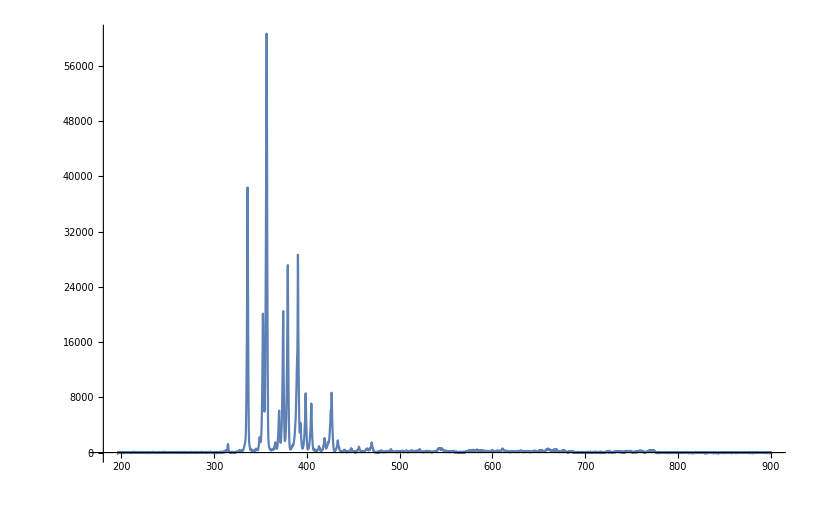

```mathematica
inputFilePath6 = "/Users/gia/Desktop/PHYS2002/Labs/N2/FLMT043001_11-38-52-208.txt";
fileContent6=Drop[Import[inputFilePath6,"Table"],14];
wavelength6 = fileContent6[[All,1]];
spectral6= fileContent6[[All,2]];
ListLinePlot[fileContent6,PlotRange -> All]
```

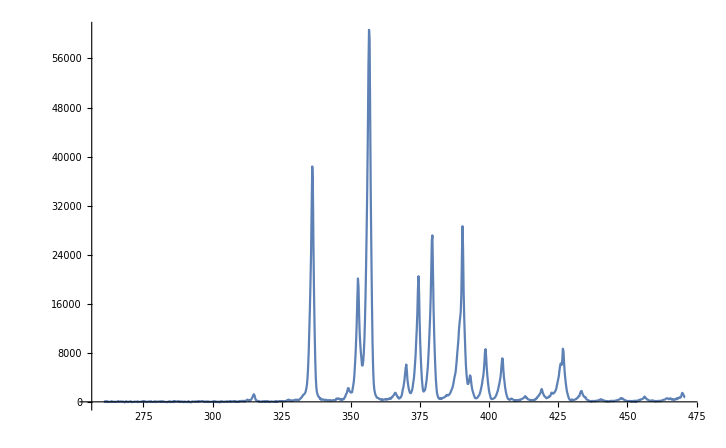

```mathematica
zoomed2= fileContent6[[300;;1300]];
 wavelength6 = zoomed2[[All,1]];
spectral6 = zoomed2[[All,2]];
ListLinePlot[zoomed2,PlotRange -> All]
```

```mathematica
FindPeaks[spectral6,0,0,8000]
```

{{352,38383.4},{430,20113.8},{449,60665.9},{534,20481.2},{558,27141.6},{610,28639.3},{650,8585.81},{785,8659.99}}

```mathematica
wavelength6[[610]]
```

390.368

```mathematica
wavelength6[[785]]
```

426.67